# L Nl Pet Site

```mathematica
generateG[t_,W_,K_]:=RandomReal[{W-t,W+t},K];

(*ml matrix:tridiagonal with random onsite+constant hopping*)
makeML[t_,W_,K_]:=Module[{g,Ox},g=generateG[t,W,K];
Ox=ConstantArray[0,{K,K}];
Do[Ox[[i,i]]=g[[i]],{i,1,K}];
Do[Ox[[i+1,i]]=t;Ox[[i,i+1]]=t,{i,1,K-1}];
Rationalize[Ox,Power[10,-20]]];

(*mnl matrix:exponential decay hopping+random onsite*)
makeMNL[t_,W_,K_,l_,c_]:=Module[{g,Ox},g=generateG[t,W,K];
Ox=Table[l/c^Abs[i-j],{i,1,K},{j,1,K}];
Do[Ox[[i,i]]=g[[i]],{i,1,K}];
Rationalize[Ox,Power[10,-20]]];

(*mpet matrix:modified Petersen graph adjacency+random onsite+exponential decay*)
makeMPET[t_,W_,K_,l_,c_]:=Module[{g,mat,p},g=generateG[t,W,K];
p=PetersenGraph[K/2,K/4];
mat=WeightedAdjacencyMatrix[p];
Do[mat[[i,i]]=g[[i]],{i,1,K}];
Do[Do[If[i=!=j,mat[[i,j]]=l*mat[[i,j]]/c^Abs[i-j]],{j,1,K}],{i,1,K}];
Normal[Rationalize[mat,Power[10,-20]]]];
```

#### Mass Spectrum

```mathematica
(*Set global parameters*)t=0.1;
c=1.0;
W=0.2;
K=12;
l=t*c;
v=0.173;
```

```mathematica
nlm=N[makeML[t,W,K],100];
nlm2=N[makeMNL[t,W,K,l,c],100];
nlm3=N[makeMPET[t,W,K,l,c],100];
ev1=Eigenvalues[nlm];ev2=Eigenvalues[nlm2];ev3=Eigenvalues[nlm3];
ec1=Inverse[Eigenvectors[nlm]];ec2=Inverse[Eigenvectors[nlm2]];ec3=Inverse[Eigenvectors[nlm3]];
```

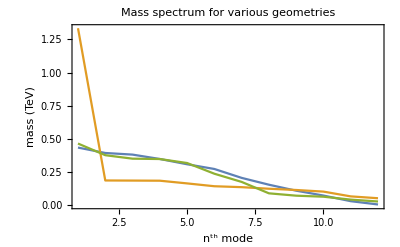

```mathematica
ListLinePlot[Abs[{ev1,ev2,ev3}],PlotRange->{{1,K},All},PlotLegends->Placed[Framed[PointLegend[{RGBColor[0.368417,0.506779,0.709798],RGBColor[0.880722,0.611041,0.142051],RGBColor[0.560181,0.691569,0.194885]},{"Local","Non-Local","Petersen"},LegendMarkers->{Style["-",FontSize->14],Style["-",FontSize->14],Style["-",FontSize->12]   },LegendMarkerSize->12,LabelStyle->{FontSize->13}],Background->Directive[White,Opacity[0.3]],FrameStyle->Gray,RoundingRadius->5,FrameMargins->0],Scaled[{0.820,0.770}]],Frame->True,FrameTicksStyle->Directive[Black,FontSize->15],FrameLabel->{Style["n^th mode",Black,FontSize->15],Style["mass (TeV)",Black,FontSize->15]},LabelStyle->Black,PlotLabel->Style["Mass spectrum for various geometries",FontSize->15]]
```

#### Cancellation Plot

```mathematica
Sum[ec1[[1,i]]*ec1[[K,i]]/(ev1[[i]]-0),{i,1,K}]
f[n_]:=Sum[ec1[[1,i]]*ec1[[K,i]]/(n+ev1[[i]]),{i,1,K}]
g[n_]:=Sum[ec2[[1,i]]*ec2[[K,i]]/(n+ev2[[i]]),{i,1,K}]
h[n_]:=Sum[ec3[[1,i]]*ec3[[K,i]]/(n+ev3[[i]]),{i,1,K}]
```

-0.12917555881868924492754637197446076971869015257789798030648530809808553189579122004744408451127477

```mathematica
Plot[{Log10[Abs[f[x]]],Log10[Abs[g[x]]],Log10[Abs[h[x]]],Log10[1/x]},{x,0,100},WorkingPrecision->80,PlotRange->{{0.1,100},All},PlotLegends->Placed[SwatchLegend[{Style["Local",Black,14],Style["Non-Local",Black,14],Style["Petersen",Black,14],Style["1/n",Black,14]},LegendFunction->(Framed[#,RoundingRadius->8,FrameStyle->Black,Background->White]&)],{1,0.5}],FrameTicksStyle->Directive[Black,FontSize->16],Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2]]
,FrameLabel->{Style["n",Black,18],Style["Log10 of ζ",Black,18]},LabelStyle->Directive[Black,14],PlotLabel->""]
```

-Graphics-